```mathematica
MyPower[p_,n_]:=MyPower[p,n] = p^n
```

```mathematica
PMinusOne[p]:=(p-1)/2
```

```mathematica
Distance[n_Integer,p_Integer, thresholdFunction_Function:Function[{x},(x-1)/2]] := Module[ {threshold, digits, position, found, nextPower, result},
If [n ==0, Return[0]];
(* Initialize some precomputed local varables *)
threshold =Evaluate[ thresholdFunction[p]];
digits = IntegerDigits[n,p];

(* find the first digit above the threshold *)
found = -1;
For[ position = 1, position <=Length[digits], position++,
If [ digits [[position]] > threshold,
found = position; Break[]
]
];

(* if we didn't find a digit, then the distance is zero *)
If [found ==-1, Return[0]];

(* we did find a faulty digit.  Now we need to look before it for digits that equal the threshold.
If we would not coun these then we would end up with a new value which is still not p-good (due
to the carrying) *)
While[ found >1,
If [ digits [[found-1]] == threshold,found --,Break[]]
];

(* if we have gone all the way to the start*)
If[found ==1,
Block[{},
nextPower= MyPower[p,(Length[digits])];
Return[nextPower-n]
]
];


nextPower=MyPower[ p,(Length[digits]+1-found)];
Return[nextPower-FromDigits[Take[digits,-(Length[digits]+1-found)],p]]
]
```

```mathematica
AlgoList[start_, end_, primes_,thresholdFunction_Function:Function[{x},(x-1)/2]] := Module[{result, current,  maxdist},

result = {};
current=start;
While[current ≤ end,
(*Print[current];*)
maxdist = Max[ParallelTable[Distance[current, p, thresholdFunction], {p, primes}]];
If[maxdist==0,
result = Append[result,current];
current +=1;
,
current += maxdist;
];
];
Return [result];
]
```

```mathematica
Timing[For[i=10^2193,i≤10^50000,i+=10^2191,Print[{i,AlgoList[IntegerPart[i-1],IntegerPart[i+10^2191],{7,11,13,19}]}]]]
```

```mathematica
Distance[6,3, Function[{x}, 7]]
```

Function[{x},7]

7

0

```mathematica
Clear[Distance]
```

```mathematica
With[
{firstPrime = 12},
With[{tuple=Prime[Range[firstPrime,firstPrime+4]]},
Table[
{firstPrime, minus, AlgoList[0,10^10,tuple, Function[{p}, (p-minus)/2]]},
{minus,1,15,2}
]
]
]
```

{{12,1,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,53,54,55,344,387,388,492,493,533,534,535,536,20683,20684,20831,20832,20833,11469519,11469520,11469521,11469522,11469523,11469524,11469750,11469751,11469752,11469753,11469754,11469755,11469791,11469792,11469793,11469794,11469795,11469796,11470121,11470122,11470123,11470124,11470125,11470126,11470127,11470164,11470165,11470166,489216516,489216517,489216518,489216519,489216520,489216521,489216522,489216523,489216524,489216525,489216561,489216562,489216563,489216564,489216565,489216566,489216567,489216568,489216608,489216676,489216677,489216678,489216719,492957031,492957032,933495435,933495436,933495437,933495438,933495439,933610603,933610640,933610641,933610642,933610643,933610644,933610645,933610646,933810629,933810630,933908619}},{12,3,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,53,54,387,492,533,534,535,20683,20831,20832,11469519,11469520,11469521,11469522,11469523,11469750,11469751,11469752,11469753,11469754,11469791,11469792,11469793,11469794,11469795,11470121,11470122,11470123,11470124,11470125,11470126,489216516,489216517,489216518,489216519,489216520,489216521,489216522,489216523,489216524,489216561,489216562,489216563,489216564,489216565,489216566,489216567,489216676,489216677}},{12,5,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,53,533,534,20831,489216516,489216517,489216518,489216519,489216520,489216521,489216522,489216523,489216561,489216562,489216563,489216564,489216565,489216566}},{12,7,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,533,489216516,489216517,489216518,489216519,489216520,489216521,489216522,489216561,489216562,489216563,489216564,489216565}},{12,9,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,489216516,489216517,489216518,489216519,489216520,489216521,489216561,489216562,489216563,489216564}},{12,11,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,489216516,489216517,489216518,489216519,489216520}},{12,13,{0,1,2,3,4,5,6,7,8,9,10,11,12}},{12,15,{0,1,2,3,4,5,6,7,8,9,10,11}}}

```mathematica
IntegerDigits[1238628316,Prime[7]]
```

{3,0,5,6,2,7,2,3}

```mathematica
Prime[12]
```

37

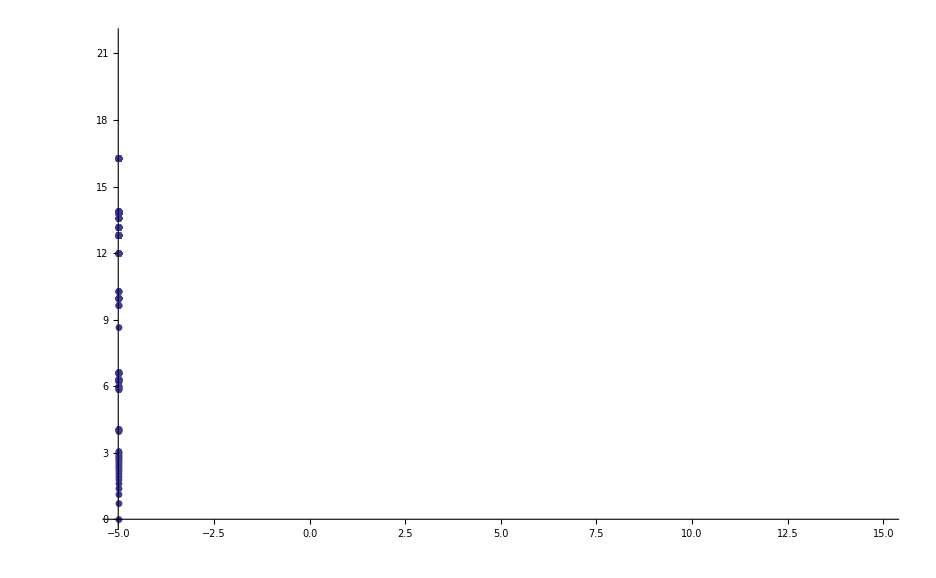

```mathematica
ListLogPlot[
With[
{firstPrime = 12},
With[{tuple=Prime[Range[firstPrime,firstPrime+4]]},
Table[
 Map[Function[{value}, {minus,value}],AlgoList[0,10^10,tuple, Function[{p}, (p-minus)/2]]],
{minus,-5,15,2}
]
]
]
, Joined->False,
PlotMarkers->Automatic,
PlotRange->{{-5,15},All},
ImageSize->Large
]
```

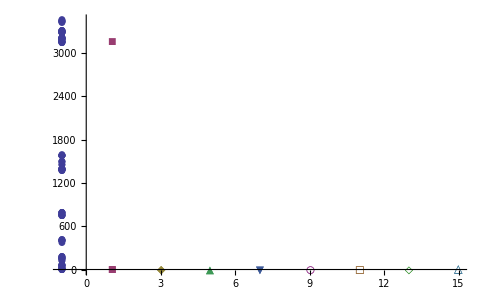

```mathematica
ListPlot[
With[
{firstPrime = 2},
With[{tuple=Prime[Range[firstPrime,firstPrime+3]]},
Table[
 Map[Function[{value}, {minus,value}],AlgoList[0,4000,tuple, Function[{p}, (p-minus)/2]]],
{minus,-1,15,2}
]
]
]
, 
PlotMarkers->Automatic
]
```

```mathematica
Table[
With[{tuple=Prime[Range[firstPrime,firstPrime+4]]},
Table[
PrintTemporary[ToString[Prime[firstPrime]] <> " - " <> ToString[minus]];{ Prime[firstPrime], minus, Length[AlgoList[0,10^12,tuple, Function[{p}, (p-minus)/2]]]},
{minus,-19,21,2}
]
]
,{firstPrime,9,20}
]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[.

KernelObject::rdead: Subkernel connected through local appears dead.

LinkObject::linkd: Unable to communicate with closed link LinkObject[.

KernelObject::rdead: Subkernel connected through local appears dead.

LinkObject::linkd: Unable to communicate with closed link LinkObject[.

General::stop: Further output of LinkObject will be suppressed during this calculation.

KernelObject::rdead: Subkernel connected through local appears dead.

General::stop: Further output of KernelObject will be suppressed during this calculation.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

$Aborted

```mathematica
ListPlot3D[ Flatten[{{{23,-5,11527},{23,-3,1849},{23,-1,249},{23,1,79},{23,3,21},{23,5,11},{23,7,9},{23,9,8},{23,11,7},{23,13,6},{23,15,5},{23,17,4},{23,19,3},{23,21,2}},{{29,-5,8333},{29,-3,2180},{29,-1,300},{29,1,89},{29,3,29},{29,5,20},{29,7,12},{29,9,11},{29,11,10},{29,13,9},{29,15,8},{29,17,7},{29,19,6},{29,21,5}},{{31,-5,8690},{31,-3,1773},{31,-1,701},{31,1,255},{31,3,130},{31,5,24},{31,7,15},{31,9,13},{31,11,11},{31,13,10},{31,15,9},{31,17,8},{31,19,7},{31,21,6}},{{37,-5,12303},{37,-3,3006},{37,-1,621},{37,1,105},{37,3,67},{37,5,35},{37,7,29},{37,9,25},{37,11,19},{37,13,13},{37,15,12},{37,17,11},{37,19,10},{37,21,9}},{{41,-5,13038},{41,-3,3653},{41,-1,1087},{41,1,262},{41,3,141},{41,5,39},{41,7,32},{41,9,19},{41,11,16},{41,13,15},{41,15,14},{41,17,13},{41,19,12},{41,21,11}},{{43,-5,7271},{43,-3,2846},{43,-1,702},{43,1,299},{43,3,100},{43,5,66},{43,7,34},{43,9,29},{43,11,26},{43,13,23},{43,15,21},{43,17,19},{43,19,17},{43,21,15}},{{47,-5,13839},{47,-3,4537},{47,-1,1139},{47,1,498},{47,3,177},{47,5,112},{47,7,54},{47,9,31},{47,11,27},{47,13,21},{47,15,19},{47,17,17},{47,19,15},{47,21,14}},{{53,-5,23618},{53,-3,10370},{53,-1,4700},{53,1,2391},{53,3,706},{53,5,337},{53,7,173},{53,9,69},{53,11,44},{53,13,30},{53,15,26},{53,17,22},{53,19,18},{53,21,17}},{{59,-5,37117},{59,-3,17718},{59,-1,7690},{59,1,3404},{59,3,1355},{59,5,552},{59,7,276},{59,9,88},{59,11,36},{59,13,34},{59,15,32},{59,17,30},{59,19,28},{59,21,26}},{{61,-5,28033},{61,-3,14018},{61,-1,7415},{61,1,3551},{61,3,1513},{61,5,726},{61,7,393},{61,9,113},{61,11,84},{61,13,53},{61,15,41},{61,17,35},{61,19,30},{61,21,27}},{{67,-5,29328},{67,-3,16657},{67,-1,7375},{67,1,3397},{67,3,1914},{67,5,930},{67,7,535},{67,9,305},{67,11,232},{67,13,126},{67,15,44},{67,17,36},{67,19,34},{67,21,32}},{{71,-5,34874},{71,-3,18087},{71,-1,10855},{71,1,5777},{71,3,3303},{71,5,2214},{71,7,1339},{71,9,649},{71,11,271},{71,13,185},{71,15,140},{71,17,102},{71,19,65},{71,21,38}}},1],Mesh->All, ImageSize->Large, ColorFunction->"DarkRainbow", InterpolationOrder->1, Method->"QuasiNewton", PerformanceGoal->"Quality", AxesLabel->{"First prime", "minus in (p-minus)/2", "count good values < 10^12"},
ViewPoint->{Back, Front,Left}, PlotRange->{All,All,{0,1500}}]
```

-Graphics3D-

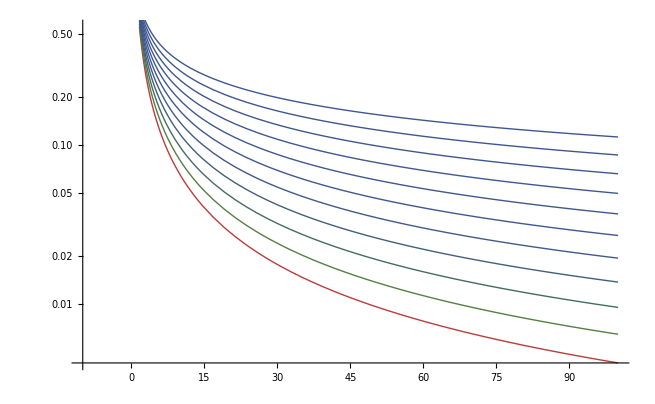

```mathematica
With[{firstPrime=10},
Show[
Table[
LogPlot[
Table[x^Sum[ Log[1/2*(p+minus)/p] / Log[p], {p,tuple}],
{tuple,{Prime[Range[firstPrime,firstPrime+4]]}}
], 
{x,-10,100},
PlotStyle->ColorData["DarkRainbow"][Abs[1/(6+minus)]]],
{minus,-5,15,2}
]
]
]
```

```mathematica
With[{firstPrime=10},
Table[FullSimplify[x^Sum[ Log[1/2*(p+1)/p] / Log[p], {p,tuple}]],
{tuple,{Prime[Range[firstPrime,firstPrime+4]]}}
]
]
```

{x^(-Log[29/15]/Log[29]-Log[31/16]/Log[31]-Log[37/19]/Log[37]-Log[41/21]/Log[41]-Log[43/22]/Log[43])}

```mathematica
FullSimplify[x^Sum[ Log[1/2*(p+1)/p] / Log[p], {p,{3,5,7,11}}]]
```

x^(-4+Log[2]/Log[3]+Log[3]/Log[5]+Log[4]/Log[7]+Log[6]/Log[11])

```mathematica
N[Log[10,14501569240339388698351211565026628791636801563979322176975372854665271047652582938955470512539223715686521822122216875463285700826971562222892729940859401285429944746479245084387125701850258486768074787121522288174095097037364107297464929213738240070646093228414030398375312938668244665767058542818707382119326875000540824123419576168829874154773891836931314700651825344078948069155552592724811634098978268353465060859966685667967853777787837218974419136220999577372200081102698486955236222663091606754421132615189595043148092125611226625080882157752086460955507143245491238162327102912074289531624407965188604404095001695867137055978827464459679448454357087702943221547878714739287643356546719071513359186000300182695276433023757236994424474345818239526704686978855309379203349788816009255597209153156768844488478985011491402150201227104202134887608604841426764863815692733433620933191656054450344365262561729169566970674784089782708527836014005568754698055074681492299328649450619771099232129826895685423994226192343905713202058817140631897490668824866945220824800058984471536592200742318410770917314168126745385373617410413292576115113563048179938355474045855309620605206941221178743815552913414185052080869702592124145494302986952793099942912612619606537257179582809122028853281655621268081227015354213432998202337066260461446640083170831336310417064143063575048193736144720469493554142799483323095245111169662171631575585689187742556125800255065810281380870038512431087039724483087268706670166698121336716671609071408577225277524096247203436122574834480548137276183462254039790011690537832231851009720278040339250411720436909294866437089019263727778745259071777699371473489580087830328642450919425232673160216394282933881341335111624709896419682098060986979424678387348771364927835653175572963495416994714604973687130139002499208867419849294509274149166874184717694716109581763674072718282581636384076924823551638654037401400744346481647402355253112901478497814909000644177531165024859044397082795683558868199292699303641174297333355436316854422678650912310119189819913427660490013829378155203478750636031317757307694950195277367696097968995809075068599613461304690719407505605422827061600276638]]
```

2200.16

```mathematica
DrieD=Flatten[{{{23,-5,11527},{23,-3,1849},{23,-1,249},{23,1,79},{23,3,21},{23,5,11},{23,7,9},{23,9,8},{23,11,7},{23,13,6},{23,15,5},{23,17,4},{23,19,3},{23,21,2}},{{29,-5,8333},{29,-3,2180},{29,-1,300},{29,1,89},{29,3,29},{29,5,20},{29,7,12},{29,9,11},{29,11,10},{29,13,9},{29,15,8},{29,17,7},{29,19,6},{29,21,5}},{{31,-5,8690},{31,-3,1773},{31,-1,701},{31,1,255},{31,3,130},{31,5,24},{31,7,15},{31,9,13},{31,11,11},{31,13,10},{31,15,9},{31,17,8},{31,19,7},{31,21,6}},{{37,-5,12303},{37,-3,3006},{37,-1,621},{37,1,105},{37,3,67},{37,5,35},{37,7,29},{37,9,25},{37,11,19},{37,13,13},{37,15,12},{37,17,11},{37,19,10},{37,21,9}},{{41,-5,13038},{41,-3,3653},{41,-1,1087},{41,1,262},{41,3,141},{41,5,39},{41,7,32},{41,9,19},{41,11,16},{41,13,15},{41,15,14},{41,17,13},{41,19,12},{41,21,11}},{{43,-5,7271},{43,-3,2846},{43,-1,702},{43,1,299},{43,3,100},{43,5,66},{43,7,34},{43,9,29},{43,11,26},{43,13,23},{43,15,21},{43,17,19},{43,19,17},{43,21,15}},{{47,-5,13839},{47,-3,4537},{47,-1,1139},{47,1,498},{47,3,177},{47,5,112},{47,7,54},{47,9,31},{47,11,27},{47,13,21},{47,15,19},{47,17,17},{47,19,15},{47,21,14}},{{53,-5,23618},{53,-3,10370},{53,-1,4700},{53,1,2391},{53,3,706},{53,5,337},{53,7,173},{53,9,69},{53,11,44},{53,13,30},{53,15,26},{53,17,22},{53,19,18},{53,21,17}},{{59,-5,37117},{59,-3,17718},{59,-1,7690},{59,1,3404},{59,3,1355},{59,5,552},{59,7,276},{59,9,88},{59,11,36},{59,13,34},{59,15,32},{59,17,30},{59,19,28},{59,21,26}},{{61,-5,28033},{61,-3,14018},{61,-1,7415},{61,1,3551},{61,3,1513},{61,5,726},{61,7,393},{61,9,113},{61,11,84},{61,13,53},{61,15,41},{61,17,35},{61,19,30},{61,21,27}},{{67,-5,29328},{67,-3,16657},{67,-1,7375},{67,1,3397},{67,3,1914},{67,5,930},{67,7,535},{67,9,305},{67,11,232},{67,13,126},{67,15,44},{67,17,36},{67,19,34},{67,21,32}},{{71,-5,34874},{71,-3,18087},{71,-1,10855},{71,1,5777},{71,3,3303},{71,5,2214},{71,7,1339},{71,9,649},{71,11,271},{71,13,185},{71,15,140},{71,17,102},{71,19,65},{71,21,38}}},1]
```

{{23,-5,11527},{23,-3,1849},{23,-1,249},{23,1,79},{23,3,21},{23,5,11},{23,7,9},{23,9,8},{23,11,7},{23,13,6},{23,15,5},{23,17,4},{23,19,3},{23,21,2},{29,-5,8333},{29,-3,2180},{29,-1,300},{29,1,89},{29,3,29},{29,5,20},{29,7,12},{29,9,11},{29,11,10},{29,13,9},{29,15,8},{29,17,7},{29,19,6},{29,21,5},{31,-5,8690},{31,-3,1773},{31,-1,701},{31,1,255},{31,3,130},{31,5,24},{31,7,15},{31,9,13},{31,11,11},{31,13,10},{31,15,9},{31,17,8},{31,19,7},{31,21,6},{37,-5,12303},{37,-3,3006},{37,-1,621},{37,1,105},{37,3,67},{37,5,35},{37,7,29},{37,9,25},{37,11,19},{37,13,13},{37,15,12},{37,17,11},{37,19,10},{37,21,9},{41,-5,13038},{41,-3,3653},{41,-1,1087},{41,1,262},{41,3,141},{41,5,39},{41,7,32},{41,9,19},{41,11,16},{41,13,15},{41,15,14},{41,17,13},{41,19,12},{41,21,11},{43,-5,7271},{43,-3,2846},{43,-1,702},{43,1,299},{43,3,100},{43,5,66},{43,7,34},{43,9,29},{43,11,26},{43,13,23},{43,15,21},{43,17,19},{43,19,17},{43,21,15},{47,-5,13839},{47,-3,4537},{47,-1,1139},{47,1,498},{47,3,177},{47,5,112},{47,7,54},{47,9,31},{47,11,27},{47,13,21},{47,15,19},{47,17,17},{47,19,15},{47,21,14},{53,-5,23618},{53,-3,10370},{53,-1,4700},{53,1,2391},{53,3,706},{53,5,337},{53,7,173},{53,9,69},{53,11,44},{53,13,30},{53,15,26},{53,17,22},{53,19,18},{53,21,17},{59,-5,37117},{59,-3,17718},{59,-1,7690},{59,1,3404},{59,3,1355},{59,5,552},{59,7,276},{59,9,88},{59,11,36},{59,13,34},{59,15,32},{59,17,30},{59,19,28},{59,21,26},{61,-5,28033},{61,-3,14018},{61,-1,7415},{61,1,3551},{61,3,1513},{61,5,726},{61,7,393},{61,9,113},{61,11,84},{61,13,53},{61,15,41},{61,17,35},{61,19,30},{61,21,27},{67,-5,29328},{67,-3,16657},{67,-1,7375},{67,1,3397},{67,3,1914},{67,5,930},{67,7,535},{67,9,305},{67,11,232},{67,13,126},{67,15,44},{67,17,36},{67,19,34},{67,21,32},{71,-5,34874},{71,-3,18087},{71,-1,10855},{71,1,5777},{71,3,3303},{71,5,2214},{71,7,1339},{71,9,649},{71,11,271},{71,13,185},{71,15,140},{71,17,102},{71,19,65},{71,21,38}}

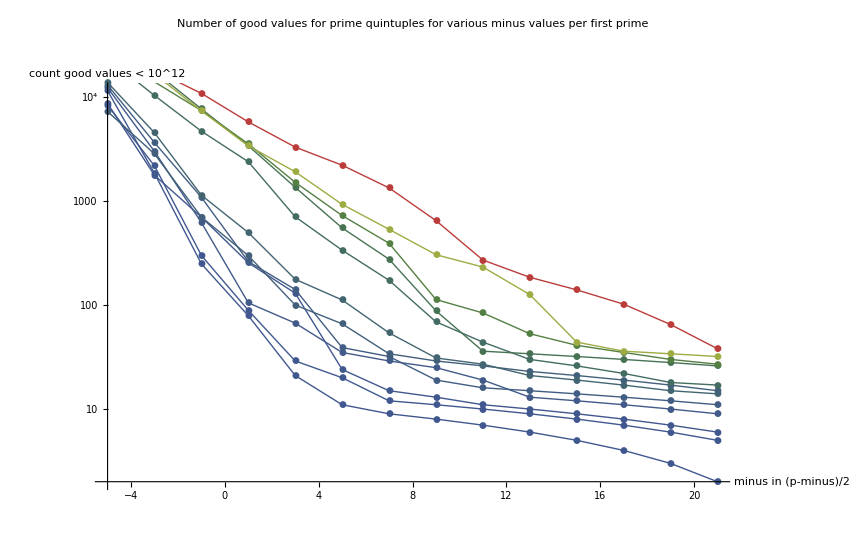

```mathematica
Show[
Table[
ListLogPlot[
Sort[Map[Rest,Select[DrieD,#[[1]]==Prime[firstPrime]&]]],
InterpolationOrder->1,
Joined->True,
PlotMarkers->Automatic,
PlotRange->All,
PlotStyle->ColorData["DarkRainbow"][1/(21-firstPrime)

]
],{firstPrime,9,20}
],
AxesLabel->{ "minus in (p-minus)/2", "count good values < 10^12"},
PlotLabel->"Number of good values for prime quintuples for various minus values per first prime"
]
```

```mathematica
Prime[9]
```

23

```mathematica
Sort[Select[DrieD,#[[1]]==Prime[9]&]]
```

{{23,-5,11527},{23,-3,1849},{23,-1,249},{23,1,79},{23,3,21},{23,5,11},{23,7,9},{23,9,8},{23,11,7},{23,13,6},{23,15,5},{23,17,4},{23,19,3},{23,21,2}}

```mathematica
Table[
{Prime[p], Prime[p+1], Prime[p+2], Prime[p+3], Prime[p+4]},{p,9,20}
]
```

{{23,29,31,37,41},{29,31,37,41,43},{31,37,41,43,47},{37,41,43,47,53},{41,43,47,53,59},{43,47,53,59,61},{47,53,59,61,67},{53,59,61,67,71},{59,61,67,71,73},{61,67,71,73,79},{67,71,73,79,83},{71,73,79,83,89}}